# Tutorial

A step-by-step introduction to the main facilities of QuEST-MMA.

Table of contents:
        • Connecting to QuEST
        • Creating quantum registers
        • Specifying gates
        • Applying circuits
        • Analysing quantum states

## Connecting to QuEST

Import the QuEST-MMA package . Further functions will be loaded once connected to an QuEST environment.

```mathematica
Import["https://quest.qtechtheory.org/QuEST.m"]
```

One then connects to a QuEST runtime environment, which can be local or remote.

```mathematica
?CreateRemoteQuESTEnv
?CreateLocalQuESTEnv
?CreateDownloadedQuESTEnv
```

CreateRemoteQuESTEnv[id] connects to the remote Igor server (on port 50000+id and 50100+id) and defines several QuEST functions, returning a link object. This should be called once. The QuEST function defintions can be cleared with DestroyQuESTEnv[link].

CreateLocalQuESTEnv[] connects to a local Mathematica backend, running single-CPU QuEST. This requires a compatible 'quest_link' executable is in the same directory as the notebook. This should be called once. The QuEST function defintions can be cleared with DestroyQuESTEnv[link].

CreateDownloadedQuESTEnv[] downloads a MacOS-CPU-QuEST server from quest.qtechtheory.org, gives it permission to run then locally connects to it. This should be called once. The QuEST function defintions can be cleared with DestroyQuESTEnv[link].

Here, we’ll automatically download the MacOS QuEST executable and locally connect.

```mathematica
env = CreateDownloadedQuESTEnv[];
```

This loads further package functions and circuit symbols, listed below.

```mathematica
?QuEST`*
```

## Creating quantum registers

Now that we’re connected to a QuEST runtime environment, we can allocate quantum registers as state vectors or density matrices.

```mathematica
numQb = 9;
ψ = CreateQureg[numQb];
ρ = CreateDensityQureg[numQb];
```

These registers are stored in the environment which may be remote. The Mathematica kernel only knows the IDs by which to identify these structures to the QuEST environment.

```mathematica
ψ
```

0

```mathematica
ρ
```

1

```mathematica
GetAllQuregs[]
```

{0,1}

This means we can create, operate on and study states that are too large to fit in Mathematica, or even this machine!

```mathematica
InitPlusState @ ψ;
CalcProbOfOutcome[ψ, 5, 1]
```

0.5

```mathematica
?InitPlusState
?CalcProbOfOutcome
```

InitPlusState[qureg] sets the qureg to state |+> (and returns the qureg id).

CalcProbOfOutcome[qureg, qubit, outcome] returns the probability of measuring qubit in the given outcome.

With some overhead, we can view the state with GetMatrix (which is initially ψ = |0⟩ and ρ = |0⟩⟨0|).

```mathematica
Dimensions @ GetMatrix[ψ]
```

{512}

```mathematica
Dimensions @ GetMatrix[ρ]
```

{512,512}

The state vectors will live in the QuEST environment until individually destroyed...

```mathematica
DestroyQureg[ψ]
DestroyQureg[ρ]
```

or all at once.

```mathematica
DestroyAllQuregs[];
```

## Specifying gates

Individual gates have syntax GateName_targetQubit  where the targetQubit index is subscript (ctrl-minus) and indexes from 0. E.g. H_3 represents a Hadamard on the 4th qubit

```mathematica
?H
```

H is the Hadamard gate.

Some gates additionally accept parameters in square brackets, e.g. Ry_2[ϕ]

```mathematica
?Ry
```

Ry[theta] is a rotation of theta around the y-axis of the Bloch sphere.

This can include matrices, e.g. U_3[(0 | ⅈ
Exp[.3ⅈ] | 0)] ...

```mathematica
?U
```

U[matrix] is a general 1 or 2 qubit unitary gate, enacting the given 2x2 or 4x4 matrix.

and lists of matrices, e.g.  Kraus_2[{ (1 | 0
0 | √(1-p)),  (0 | √p
0 | 0)}] ...

```mathematica
?Kraus
```

Kraus[ops] applies a one or two-qubit Kraus map (given as a list of Kraus operators) to a density matrix.

Multiple target qubits are comma separated, or supplied as a list, e.g. SWAP_(0,3) and M_(0,1,2,3) ...

```mathematica
?SWAP
?M
```

SWAP is a 2 qubit gate which swaps the state of two qubits.

M is a desctructive measurement gate which measures the indicated qubits in the Z basis.

unless specified as Pauli sequences, e.g. R[ϕ, X_2 Y_3 Z_0]

```mathematica
?R
```

R[theta, paulis]W is the unitary Exp[-i θ/2 paulis].

Controlled gates are merely wrapped in C_(control qubits)[ ],   e.g. C_(1,2)[ X_3] is a doubly-controlled NOT

```mathematica
Subscript[C, 0,1,2][Subscript[U, 6,3][({{ⅇ^(ⅈ π/3), 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})]];
```

Some operations like decoherence are only relevant for density matrices (states created with createDensityQureg)

```mathematica
?Deph
?Depol
?Damp
?Kraus
```

Deph[prob] is a 1 or 2 qubit dephasing with probability prob of error.

Depol[prob] is a 1 or 2 qubit depolarising with probability prob of error.

Damp[prob] is 1 qubit amplitude damping with the givern decay probability.

Kraus[ops] applies a one or two-qubit Kraus map (given as a list of Kraus operators) to a density matrix.

## Applying circuits

A circuit can be written verbosely as a list (to be applied left-to-right) of gates...

```mathematica
{Subscript[H, 2], Subscript[Rz, 1][.3], Subscript[C, 4][Subscript[X, 3]],  Subscript[C, 0,1,2][Subscript[SWAP, 4,5]]};
DrawCircuit[%]
```

-Graphics-

or concisely as a direct product wrapped in Circuit[] to prevent automatic commutation (or to be reversed, Operator[] )

```mathematica
Circuit[ Subscript[H, 2] Subscript[Rz, 1][.3] Subscript[C, 4][Subscript[X, 3]] Subscript[C, 0,1,2][Subscript[SWAP, 4,5]] ]
```

{H_2,Rz_1[0.3],C_4[X_3],C_(0,1,2)[SWAP_(4,5)]}

```mathematica
Operator[ Subscript[H, 2] Subscript[Rz, 1][.3] Subscript[C, 4][Subscript[X, 3]] Subscript[C, 0,1,2][Subscript[SWAP, 4,5]] ]
```

{C_(0,1,2)[SWAP_(4,5)],C_4[X_3],Rz_1[0.3],H_2}

Circuits can be specified in terms of symbols/parameters, though which must be assigned numerical values before simulation.

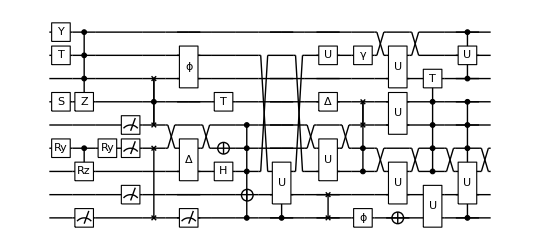

```mathematica
m1 = ({{0, ⅈ}, {Exp[.3ⅈ], 0}});
m2 = ({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});

u[θ_]:= Circuit[
 Subscript[S, 5] Subscript[T, 7] Subscript[Y, 8] Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]]Subscript[C, 8,7,6][Subscript[Z, 5]] Subscript[M, 0] Subscript[Ry, 3][θ] Subscript[M, 1,3,4] Subscript[SWAP, 0,3] Subscript[C, 5][Subscript[SWAP, 4,6]]Subscript[Depol, 2,4][θ/100] Subscript[Deph, 7,6][θ/400] Subscript[M, 0] Subscript[H, 2] Subscript[X, 3] Subscript[T, 5] Subscript[C, 0,2,3,4][Subscript[X, 1]] Subscript[C, 0][Subscript[U, 1,7][m2]]Subscript[U, 2,4][m2] Subscript[U, 7][m1]  Subscript[SWAP, 0,1] Subscript[Depol, 5][θ/300] Subscript[Deph, 0][θ/200]   Subscript[Damp, 7][θ/500] Subscript[C, 2,3][Subscript[SWAP, 4,5]] Subscript[U, 3,1][m2] Subscript[U, 4,5][m2] Subscript[U, 6,8][m2] Subscript[X, 0]  Subscript[U, 0,1][m2] Subscript[C, 2,3,4,5][Subscript[T, 6]] Subscript[C, 0,2,4,5][Subscript[U, 1,3][m2]]Subscript[C, 6,8][Subscript[U, 7][m1]] 
];

DrawCircuit @ u[θ]
```

Circuits can be applied to instantiated quantum registers through ApplyCircuit

```mathematica
ψ = CreateQureg[3];
ApplyCircuit[ Circuit[Subscript[H, 0] Subscript[X, 1] Subscript[Ry, 2][π/3]], ψ];
GetMatrix[ψ]
```

{0.+0. ⅈ,0.+0. ⅈ,0.612372+0. ⅈ,0.612372+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.353553+0. ⅈ,0.353553+0. ⅈ}

```mathematica
?ApplyCircuit
```

ApplyCircuit[circuit, qureg] modifies qureg by applying the circuit. Returns any measurement outcomes, grouped by M operators and ordered by their order in M.
ApplyCircuit[circuit, inQureg, outQureg] leaves inQureg unchanged, but modifies outQureg to be the result of applying the circuit to inQureg.

ApplyCircuit returns a list of the random measurement outcomes (if any), ordered and grouped by the ordering of M in the circuit

```mathematica
ApplyCircuit[ Circuit[ Subscript[M, 0] Subscript[M, 1,2]], ψ]
```

{{1},{1,0}}

Remember these measurements are destructive

```mathematica
ApplyCircuit[ Circuit[ Subscript[M, 0,1,2]], ψ]
```

{{1,1,0}}

Remember that symbols/parameters in the circuit must be given numerical values before evaluation

```mathematica
ApplyCircuit[ Subscript[Rx, 0][ϕ], ψ]
```

Error:  Circuit contains non-numerical parameters!

$Failed

Circuits applied to density matrices are no different

```mathematica
ApplyCircuit[u[0], InitPlusState @ CreateDensityQureg[9]]
```

{{1},{1,0,1},{0}}

## Analysing quantum states

```mathematica
DestroyAllQuregs[];
```

Quantum registers can be studied without expensively copying their state vector or density matrix to Mathematica from the QuEST environment.

```mathematica
ρ = InitPlusState @ CreateDensityQureg @ numQb;
ApplyCircuit[ Subscript[Depol, 0,1][.1], ρ];
CalcPurity[ρ]
?CalcPurity
```

0.848533

CalcPurity[qureg] returns the purity of the given density matrix.

```mathematica
ψ = InitPlusState @ CreateQureg @ numQb;
CalcFidelity[ρ, ψ]
?CalcFidelity
```

0.92

CalcFidelity[qureg1, qureg2] returns the fidelity between the given states.

```mathematica
CalcProbOfOutcome[ρ, 0, 0]
ApplyCircuit[ Subscript[Damp, 0][.1], ρ];
CalcProbOfOutcome[ρ, 0, 0]
?CalcProbOfOutcome
```

0.5

0.55

CalcProbOfOutcome[qureg, qubit, outcome] returns the probability of measuring qubit in the given outcome.

This allows us to express complicated calculations succinctly, and evaluate them quickly.

```mathematica
ApplyCircuit[u[0],InitPlusState @ ψ];

params = Range[0,π,.01];
fids = Table[
	ApplyCircuit[u[θ],InitPlusState @ ρ];
	CalcFidelity[ρ, ψ],
	{θ, params}
];
```

Here we’ve calculated how smoothly varying the noise level θ in our complicated u[θ] circuit (drawn here) affects the fidelity with its initial |+⟩⟨+| state. Note the results here are random since our circuit contains projective measurement gates.

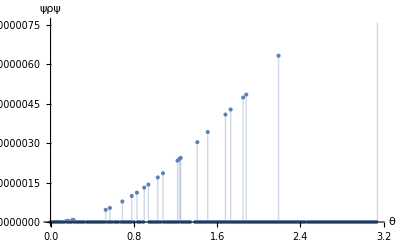

```mathematica
ListPlot[
	Transpose[{params,fids}], 
	AxesLabel-> {"θ","ψρψ"},
	Filling->Bottom
]
```

Finally, we free the state-vectors from the QuEST environment and disconnect from quest_link (killing the process).

```mathematica
DestroyAllQuregs[]; 
DestroyQuESTEnv[env];
```